```mathematica
SetDirectory @ NotebookDirectory[];
<<Rotation.m
<<Linearize.m
<<PlotCustom.m
<<NotationRules.m
```

## CINEMÁTICA

-Graphics-

### MATRIZES DE ROTAÇÃO (N ↔ E)

```mathematica
Subscript[ℝ, "E"]^("N") = Rotation["z", "x"][ψ[t], ϕ[t]];
Subscript[ℝ, "N"]^("E") = Transpose[Subscript[ℝ, "E"]^("N")];
```

```mathematica
Subscript[ℝ, "E"]^("N")//TraditionalForm
```

(cos(ψ(t)) | sin(ψ(t)) (-cos(ϕ(t))) | sin(ψ(t)) sin(ϕ(t))
sin(ψ(t)) | cos(ψ(t)) cos(ϕ(t)) | -cos(ψ(t)) sin(ϕ(t))
0 | sin(ϕ(t)) | cos(ϕ(t)))

### POSIÇÃO DO CENTRO DE MASSA

```mathematica
Subscript[p, "C/O"]^("N") = {x[t], y[t], 0}; 
Subscript[p, "G/C"]^("E") = {0, 0, -r};
Subscript[p, "G/O"]^("N") = Subscript[ℝ, "E"]^("N").Subscript[p, "G/C"]^("E") + Subscript[p, "C/O"]^("N")
```

{-r Sin[ϕ[t]] Sin[ψ[t]]+x[t],r Cos[ψ[t]] Sin[ϕ[t]]+y[t],-r Cos[ϕ[t]]}

### VELOCIDADES ANGULARES

```mathematica
Subscript[ω, "a"]^("E") = Subscript[ℝ, "N"]^("E").{0, 0, ψ'[t]} + {ϕ'[t], 0, 0}
Subscript[ω, "r"]^("E")= {0, θ'[t], 0}
ω^("E") =Subscript[ω, "a"]^("E") + Subscript[ω, "r"]^("E")
```

{ϕ'[t],Sin[ϕ[t]] ψ'[t],Cos[ϕ[t]] ψ'[t]}

{0,θ'[t],0}

{ϕ'[t],θ'[t]+Sin[ϕ[t]] ψ'[t],Cos[ϕ[t]] ψ'[t]}

### VELOCIDADE DO CENTRO DE MASSA

```mathematica
Subscript[v, "G"]^("N") = D[Subscript[p, "G/O"]^("N"),t] // FullSimplify
Subscript[v, "G"]^("E") = ω^("E")×(Subscript[p, "G/C"]^("E")) // FullSimplify
```

{x'[t]-r (Cos[ϕ[t]] Sin[ψ[t]] ϕ'[t]+Cos[ψ[t]] Sin[ϕ[t]] ψ'[t]),y'[t]+r Cos[ϕ[t]] Cos[ψ[t]] ϕ'[t]-r Sin[ϕ[t]] Sin[ψ[t]] ψ'[t],r Sin[ϕ[t]] ϕ'[t]}

{-r (θ'[t]+Sin[ϕ[t]] ψ'[t]),r ϕ'[t],0}

### EQUAÇÃO DE VÍNCULO

```mathematica
ce = Solve[Subscript[v, "G"]^("N") == Subscript[ℝ, "E"]^("N").Subscript[v, "G"]^("E"), {x'[t],y'[t]}] //First
```

{x'[t]→-r Cos[ψ[t]] θ'[t],y'[t]→-r Sin[ψ[t]] θ'[t]}

### VELOCIDADE DO PONTO C

```mathematica
Subscript[v, "C"]^("N") = {x'[t], y'[t], 0} /. ce
Subscript[v, "C"]^("E") = Subscript[ℝ, "N"]^("E") . Subscript[v, "C"]^("N") // FullSimplify
```

{-r Cos[ψ[t]] θ'[t],-r Sin[ψ[t]] θ'[t],0}

{-r θ'[t],0,0}

## DINÂMICA

### TQMA – POLO C

```mathematica
Subscript[𝕀, "C"]^("E") = DiagonalMatrix[{i+1, j+1, i}] m r^2;
Subscript[H, "C"]^("E") = (Subscript[𝕀, "C"]^("E").ω^("E"))
Subscript[M, "C"]^("E") = Subscript[p, "G/C"]^("E") ×(Subscript[ℝ, "N"]^("E").{0, 0, m g})
```

{(1+i) m r^2 ϕ'[t],(1+j) m r^2 (θ'[t]+Sin[ϕ[t]] ψ'[t]),i m r^2 Cos[ϕ[t]] ψ'[t]}

{g m r Sin[ϕ[t]],0,0}

```mathematica
TQMA = (D[Subscript[H, "C"]^("E"), t] + Subscript[ω, "a"]^("E")×Subscript[H, "C"]^("E") + Subscript[v, "C"]^("E")×(m Subscript[v, "G"]^("E")) - Subscript[M, "C"]^("E")) // FullSimplify;
TQMA /. notation // TableForm
```

m r (-((1+j) r θ̇ ψ̇ c_ϕ)-g s_ϕ+(-1+i-j) r (ψ̇)^2 c_ϕ s_ϕ+(1+i) r ϕ'')
m r^2 ((2+j) ϕ̇ ψ̇ c_ϕ+(1+j) (θ''+s_ϕ ψ''))
m r^2 (j θ̇ ϕ̇+(-2 i+j) ϕ̇ ψ̇ s_ϕ+i c_ϕ ψ'')

### EQUAÇÕES DIFERENCIAIS DE MOVIMENTO

```mathematica
EOMa[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMA,
	{ψ''[t], ϕ''[t], θ''[t]}
	] // Collect[#, {ψ'[t], ϕ'[t], θ'[t]}, FullSimplify]&;
EOMa[t] // TableForm
```

ψ''[t]→-(j Sec[ϕ[t]] θ'[t] ϕ'[t])/i+((2 i-j) Tan[ϕ[t]] ϕ'[t] ψ'[t])/i
ϕ''[t]→(g Sin[ϕ[t]])/(r+i r)+((1+j) Cos[ϕ[t]] θ'[t] ψ'[t])/(1+i)+((1-i+j) Cos[ϕ[t]] Sin[ϕ[t]] ψ'[t]^2)/(1+i)
θ''[t]→(j Tan[ϕ[t]] θ'[t] ϕ'[t])/i+(((-1+i-j) j Cos[ϕ[t]]+(1+j) (-2 i+j) Sec[ϕ[t]]) ϕ'[t] ψ'[t])/(i (1+j))

```mathematica
EOMa[t] /. notation // FullSimplify // TableForm
```

ψ''→-(ϕ̇ (j θ̇+(-2 i+j) ψ̇ s_ϕ))/(i c_ϕ)
ϕ''→(g s_ϕ+r ψ̇ c_ϕ ((1+j) θ̇+(1-i+j) ψ̇ s_ϕ))/((1+i) r)
θ''→(ϕ̇ (ψ̇ (-((2 i-j) (1+j))+(-1+i-j) j c_ϕ^2)+j (1+j) θ̇ s_ϕ))/(i (1+j) c_ϕ)

### SOLUÇÕES EM REGIME PERMANENTE

```mathematica
RPcond = {ψ''[t] -> 0, ϕ''[t] -> 0, θ''[t] -> 0, ψ'[t] -> Subscript[Ω, "y"], ϕ'[t] -> 0, θ'[t] -> Subscript[Ω, "s"], ϕ[t] -> SuperStar[ϕ], g -> r Subscript[Ω, "p"]^2};
TQMA/. RPcond
```

{m r (-r Sin[ϕ^*] Ω_p^2-(1+j) r Cos[ϕ^*] Ω_s Ω_y+(-1+i-j) r Cos[ϕ^*] Sin[ϕ^*] Ω_y^2),0,0}

```mathematica
RPsol = Solve[(# == 0)& /@ (TQMA/. RPcond), {Subscript[Ω, "s"]}] //First //FullSimplify
```

{Ω_s→((-1+i-j) Sin[ϕ^*] Ω_y^2-Ω_p^2 Tan[ϕ^*])/((1+j) Ω_y)}

```mathematica
PAR = {i -> 1/4, j-> 1/2, Subscript[Ω, "p"]-> 1};
```

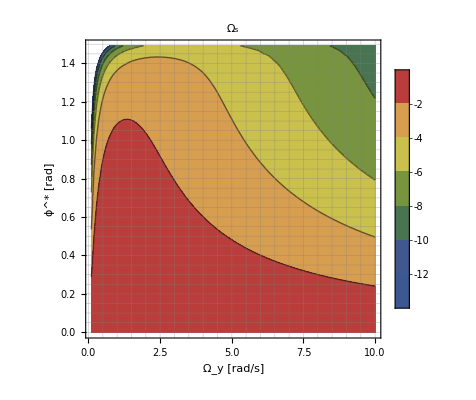

```mathematica
ContourPlot[Subscript[Ω, "s"]/.RPsol/.PAR,{Subscript[Ω, "y"],0.1, 10},{SuperStar[ϕ],0,0.95 π/2},
PlotTheme->"Detailed",ColorFunction->"DarkRainbow",GridLines->{Range[0,10,0.5],Range[0,1.50,0.05]}, 
PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20}],FrameLabel->{"Ω_y [rad/s]","ϕ^* [rad]"}, PlotLabel->"Ω_s"]
```

```mathematica
TQMA/. RPcond /.{Subscript[Ω, "y"]->0}
```

{-m r^2 Sin[ϕ^*] Ω_p^2,0,0}

```mathematica
TQMA/. RPcond/. RPsol //Simplify
```

{0,0,0}

```mathematica
Subscript[v, "G"]^("E") /. RPcond // FullSimplify
```

{-r (Ω_s+Sin[ϕ^*] Ω_y),0,0}

### LINEARIZAÇÃO

```mathematica
TQMAL = Linearize[TQMA, RPcond] /.RPsol //Simplify;
```

```mathematica
EOMl[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMAL,
	{ψ''[t], ϕ''[t], θ''[t]}
	] // Collect[#, {ψ'[t], ϕ'[t], θ'[t]}, FullSimplify]&;
EOMl[t] // TableForm
```

ψ''[t]→((j Sec[ϕ^*] Ω_p^2+i (2+j) Ω_y^2) Tan[ϕ^*] ϕ'[t])/(i (1+j) Ω_y)
ϕ''[t]→(Sec[ϕ^*] Ω_p^2 ϕ[t]+(1-i+j) Cos[ϕ^*]^2 Ω_y^2 ϕ[t])/(1+i)+((1+j) Cos[ϕ^*] Ω_y θ'[t])/(1+i)+(Sin[ϕ^*] (-Ω_p^2+(1-i+j) Cos[ϕ^*] Ω_y^2) ψ'[t])/((1+i) Ω_y)
θ''[t]→-((i (2+j) Sec[ϕ^*] Ω_y^2+j Ω_p^2 Tan[ϕ^*]^2) ϕ'[t])/(i (1+j) Ω_y)

## MODELO MATEMÁTICO - FORMA DE ESPAÇO DE ESTADOS

### MATRIZ DE ESTADOS 𝔸

```mathematica
𝕩[t_] = {ϕ[t], ψ'[t], ϕ'[t], θ'[t]};
𝔸 = CoefficientArrays[𝕩'[t]/.EOMl[t], 𝕩[t]][[2]] // Normal;
𝔸 // MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | ((j Sec[ϕ^*] Ω_p^2+i (2+j) Ω_y^2) Tan[ϕ^*])/(i (1+j) Ω_y) | 0
(Sec[ϕ^*] Ω_p^2)/(1+i)+((1-i+j) Cos[ϕ^*]^2 Ω_y^2)/(1+i) | (Sin[ϕ^*] (-Ω_p^2+(1-i+j) Cos[ϕ^*] Ω_y^2))/((1+i) Ω_y) | 0 | ((1+j) Cos[ϕ^*] Ω_y)/(1+i)
0 | 0 | -(i (2+j) Sec[ϕ^*] Ω_y^2+j Ω_p^2 Tan[ϕ^*]^2)/(i (1+j) Ω_y) | 0)

### ANÁLISE DE ESTABILIDADE

```mathematica
𝔸 /. PAR //MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | (8 (Sec[ϕ^*]/2+(5 Ω_y^2)/8) Tan[ϕ^*])/(3 Ω_y) | 0
(4 Sec[ϕ^*])/5+Cos[ϕ^*]^2 Ω_y^2 | (4 Sin[ϕ^*] (-1+5/4 Cos[ϕ^*] Ω_y^2))/(5 Ω_y) | 0 | 6/5 Cos[ϕ^*] Ω_y
0 | 0 | -(8 (5/8 Sec[ϕ^*] Ω_y^2+1/2 Tan[ϕ^*]^2))/(3 Ω_y) | 0)

```mathematica
Eigenvalues[𝔸 /. PAR]//TableForm
```

0
0
-(4 ⅈ √(2/15) Cos[ϕ^*]^3 √(32-32 Cos[2 ϕ^*]-24 Cos[ϕ^*] Ω_y^2-24 Cos[3 ϕ^*] Ω_y^2+25 Ω_y^4+30 Cos[2 ϕ^*] Ω_y^4+5 Cos[4 ϕ^*] Ω_y^4))/(√(35+56 Cos[2 ϕ^*]+28 Cos[4 ϕ^*]+8 Cos[6 ϕ^*]+Cos[8 ϕ^*]) Ω_y)
(4 ⅈ √(2/15) Cos[ϕ^*]^3 √(32-32 Cos[2 ϕ^*]-24 Cos[ϕ^*] Ω_y^2-24 Cos[3 ϕ^*] Ω_y^2+25 Ω_y^4+30 Cos[2 ϕ^*] Ω_y^4+5 Cos[4 ϕ^*] Ω_y^4))/(√(35+56 Cos[2 ϕ^*]+28 Cos[4 ϕ^*]+8 Cos[6 ϕ^*]+Cos[8 ϕ^*]) Ω_y)

```mathematica
EIG[deg_]:= Show[
	Plot[
		Sort@(Re/@Eigenvalues[𝔸 /. PAR /.{SuperStar[ϕ]-> deg π/180, Subscript[Ω, "y"]-> yr}]), {yr,0,2}, PlotRange->{-2,+2}, 
		PlotStyle->Cool⟦1⟧, GridLines->Automatic, Frame->True, FrameLabel->{"Ω_y (rad/s)",None},
		PlotLabel->"Eigenvalues of disc model (ϕ^* = "<>ToString[deg]<>".ba)",
		PlotLegends->Placed[LineLegend[{"Re (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}], Before],
		ImageSize->{450,450},
		AspectRatio->1
		],
	Plot[
		Sort@(*RedundantElim@*)Chop@(Im/@Eigenvalues[𝔸 /. PAR /.{SuperStar[ϕ]-> deg π/180, Subscript[Ω, "y"]-> yr}]),{yr,0,2}, 
		PlotStyle->{Cool⟦3⟧,Dashed},
		PlotLegends-> Placed[LineLegend[{"Im (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}],Before]
		]
	]
```

```mathematica
Manipulate[EIG[ϕ],{ϕ,Range[0,30,2]},ControlType-> Setter]
```

## EXPORT TO OCTAVE

### RULES

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};
```

### EXPORT FILE

```mathematica
fileD = OpenWrite["export/disc_OCT.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩'[t]/.EOMa[t](*Join[𝕣𝕢[t], EOM2[t]]*)/.PAR)], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```